### Programa para leer datos .txt obtenidos en CST

```mathematica
lambdaRange=Range[400,700,50];
```

```mathematica
(*Funcion para importar los datos*)
importDataC[dir_]:=Module[{data,freq,lambda,lambda0,dataCabs0,dataCsca0,dataCabs,dataCsca},
data=Import[dir];
freq=Drop[Drop[data[[All,1]],{1,5}],{8,19}];
lambda=0.2418*h c/freq;
lambda0=Range[700,400,-50];
dataCabs0=Drop[Drop[data[[All,2]],{1,5}],{8,19}];
dataCsca0=Drop[data[[All,2]],{1,17}];
dataCabs=Sort[Transpose[{lambda0,dataCabs0}]];
dataCsca=Sort[Transpose[{lambda0,dataCsca0}]];{dataCabs,dataCsca}]
```

```mathematica
importDataQ[dir_]:=Module[{data,freq,lambda,lambda0,dataCabs0,dataCsca0,dataCabs,dataCsca},
data=Import[dir];
freq=Drop[Drop[data[[All,1]],{1,5}],{8,19}];
lambda=0.2418*h c/freq;
lambda0=Range[700,400,-50];
dataCabs0=Drop[Drop[data[[All,2]],{1,5}],{8,19}]/(Pi*(2680)^2);
dataCsca0=Drop[data[[All,2]],{1,17}]/(Pi*(2680)^2);
dataCabs=Sort[Transpose[{lambda0,dataCabs0}]];
dataCsca=Sort[Transpose[{lambda0,dataCsca0}]];{dataCabs,dataCsca}]
```

```mathematica
(*Funcion error absoluto*)
```

```mathematica
errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]
errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Background

```mathematica
bck1000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\1000.csv"];
bck1500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\1500.csv"];
bck2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\2000.csv"];
bck2500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\2500.csv"];
```

```mathematica
eriCabsMie=Table[{λ,mieQabs[nindexEri30[λ],1.8235,2680,λ][[3]]},{λ,400,700,50}];
eriCscaMie=Table[{λ,mieQsca[nindexEri30[λ],1.8235,2680,λ][[3]]},{λ,400,700,50}];
eriQabsMie=Table[{λ,mieQabs[nindexEri30[λ],1.8235,2680,λ][[4]]},{λ,400,700,50}];
eriQscaMie=Table[{λ,mieQsca[nindexEri30[λ],1.8235,2680,λ][[4]]},{λ,400,700,50}];
```

```mathematica
error1Abs=errorAbs[bck1000[[1]][[All,2]],eriCabsMie[[All,2]]]
error2Abs=bck1500[[1]][[All,2]]-eriCabsMie[[All,2]];
error3Abs=bck2000[[1]][[All,2]]-eriCabsMie[[All,2]];
error1Sca=bck1000[[2]][[All,2]]-eriCscaMie[[All,2]];
error2Sca=bck1500[[2]][[All,2]]-eriCscaMie[[All,2]];
error3Sca=bck2000[[2]][[All,2]]-eriCscaMie[[All,2]];
```

{6.35071×10^6,2.61035×10^6,643812.,2.03332×10^6,736226.,239646.,83979.5}

```mathematica
Mean[errorAbs[bck1000[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck1500[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck2000[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck2500[[1]][[All,2]],eriCabsMie[[All,2]]]]
```

2.32467×10^6

2.32467×10^6

2.32467×10^6

«1 more identical outputs»

```mathematica
Mean[errorAbs[bck1000[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck1500[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck2000[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck2500[[2]][[All,2]],eriCscaMie[[All,2]]]]
```

1.8759×10^7

1.8759×10^7

1.88471×10^7

1.90222×10^7

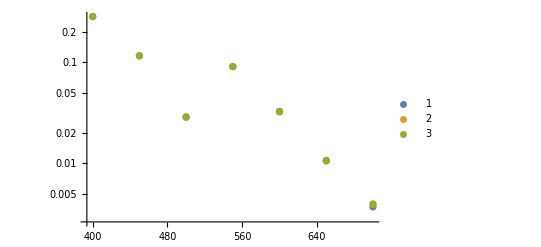

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[bck1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2500[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

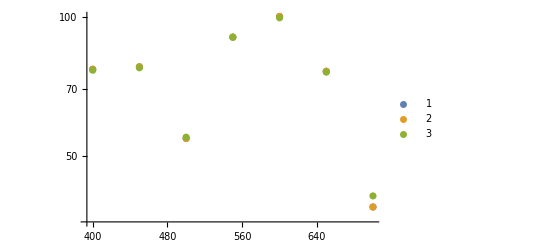

```mathematica
ListPlot[{Transpose[{lambdaRange,errorRel[bck1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck1500[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

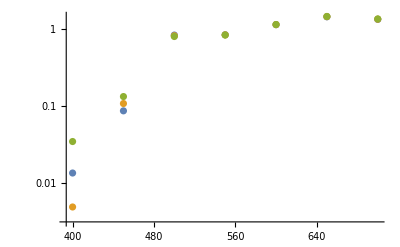

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[bck1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2500[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All]
```

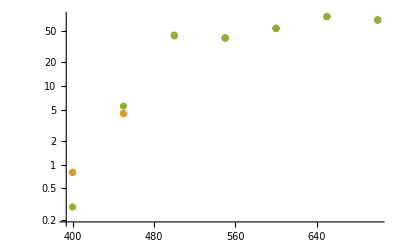

```mathematica
ListPlot[{Transpose[{lambdaRange,errorRel[bck1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All]
```

## PML

```mathematica
pml1000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\1000.csv"];
pml1500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\1500.csv"];
pml2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\2000.csv"];
pml2500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\2500.csv"];
```

```mathematica
pmlBCK2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML_BCK_2000.csv"];
```

```mathematica
pmlBCK2000[[1]]
```

{{400,1.45813×10^7},{450,5.95217×10^6},{500,1.8209×10^6},{550,4.28091×10^6},{600,1.47043×10^6},{650,553468.},{700,299843.},{750,191972.},{800,138733.}}

```mathematica
Mean[errorAbs[pml1000[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml1500[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml2500[[1]][[All,2]],eriQabsMie[[All,2]]]]
```

0.0801659

0.0803932

0.0801458

0.0802124

```mathematica
Mean[errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml1500[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml2000[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml2500[[2]][[All,2]],eriQscaMie[[All,2]]]]
```

0.805211

0.807146

0.809206

0.816287

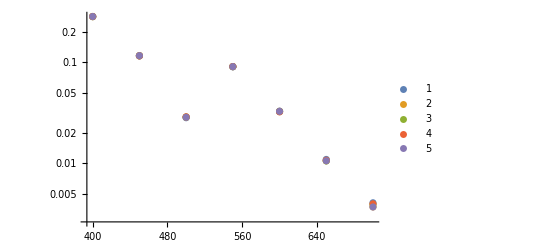

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml1500[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2500[[1]][[All,2]],eriQabsMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

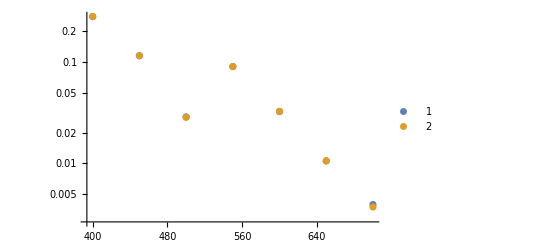

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

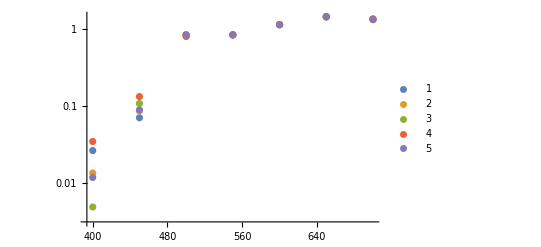

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2000[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pml2500[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All,PlotLegends->Automatic]
```

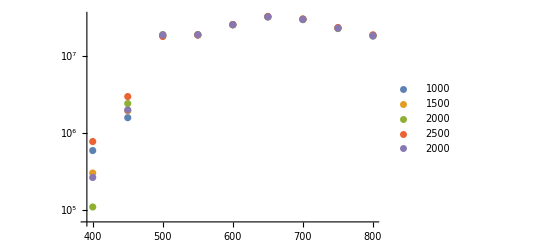

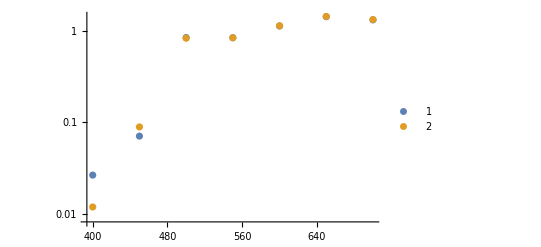

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All,PlotLegends->Automatic]
```

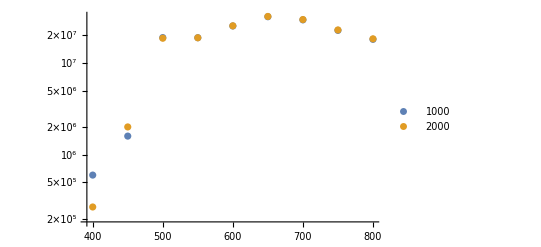

```mathematica
0.2418*h c/0.611821343
```

490.341

## Mesh

```mathematica
0.2418*h c/0.66620546222222
```

450.314

```mathematica
mesh150015002520=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_25_20.csv"];
lambda0mesh150015002520=Range[700,400,-50];
lambda1mesh150015002520=Range[700,500,-50];
dataCabs0mesh150015002520=Drop[Drop[mesh150015002520[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh150015002520=Sort[Transpose[{lambda0mesh150015002520,dataCabs0mesh150015002520}]]
dataCsca0mesh150015002520=Drop[mesh150015002520[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh1500150025200=Sort[Transpose[{lambda1mesh150015002520,dataCsca0mesh150015002520}]]
```

{{400,0.670151},{450,0.284396},{500,0.108743},{550,0.188632},{600,0.0614393},{650,0.024481},{700,0.0189341}}

{{500,1.53597},{550,1.65261},{600,1.95709},{650,2.25416},{700,2.51836}}

```mathematica
mesh150015002015=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_20_15.csv"];
lambda0mesh150015002015=Range[700,400,-50];
lambda1mesh150015002015=Range[700,500,-50];
dataCabs0mesh150015002015=Drop[Drop[mesh150015002015[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh150015002015=Sort[Transpose[{lambda0mesh150015002015,dataCabs0mesh150015002015}]]
dataCsca0mesh150015002015=Drop[mesh150015002015[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh1500150020150=Sort[Transpose[{lambda1mesh150015002015,dataCsca0mesh150015002015}]]
```

{{400,0.670151},{450,0.284396},{500,0.108743},{550,0.188632},{600,0.0614393},{650,0.024481},{700,0.0189341}}

{{500,1.53597},{550,1.65261},{600,1.95709},{650,2.25416},{700,2.51836}}

```mathematica
mesh15001500nolocal=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_no_local.csv"];
lambda0mesh15001500nolocal=Range[700,400,-50];
lambda1mesh15001500nolocal=Range[700,500,-50];
dataCabs0mesh15001500nolocal=Drop[Drop[mesh15001500nolocal[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh15001500nolocal=Sort[Transpose[{lambda0mesh15001500nolocal,dataCabs0mesh15001500nolocal}]]
dataCsca0mesh15001500nolocal=Drop[mesh15001500nolocal[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh15001500nolocal0=Sort[Transpose[{lambda1mesh15001500nolocal,dataCsca0mesh15001500nolocal}]]
```

{{400,0.669809},{450,0.284259},{500,0.108695},{550,0.188551},{600,0.0614007},{650,0.0244477},{700,0.0189088}}

{{500,1.53716},{550,1.65329},{600,1.956},{650,2.25344},{700,2.51845}}

```mathematica
dataCscamesh1500200020151=Transpose[{{400,450},{34652962.044491/(Pi*(2680)^2),37396871.024578/(Pi*(2680)^2)}}]
dataCscamesh1500200025201=Transpose[{{400,450},{34652962.044491/(Pi*(2680)^2),37396871.024578/(Pi*(2680)^2)}}]
dataCscamesh15002000nolocal1=Transpose[{{400,450},{34670770.635787/(Pi*(2680)^2),37406178.563308/(Pi*(2680)^2)}}]
```

{{400,1.53575},{450,1.65736}}

{{400,1.53575},{450,1.65736}}

{{400,1.53654},{450,1.65777}}

```mathematica
dataCscamesh150020002015=Join[dataCscamesh1500200020151,dataCscamesh1500150020150];
dataCscamesh150020002520=Join[dataCscamesh1500200025201,dataCscamesh1500150025200];
dataCscamesh15002000nolocal=Join[dataCscamesh15002000nolocal1,dataCscamesh15001500nolocal0];
```